```mathematica
ClearAll["Global`*"] (* clear variables *)

(* switch off message that solar panels cannot be lower than 0 degrees *)
Off[FindMinimum::reged];
Off[FindMaximum::reged];

(* clear days at ~25 angle: 13/5, 19/7, 17/8 *)

(* Adjusting the solar panels x times a day
The times are evenly spread over the time the sun is up *)
year = 2016;

(* parameters are forced numeric, so findMaximum in dayangle works better *)
angle[i_?NumericQ,a_?NumericQ,d_]:= ( (* params: index of sunPositions table, solar panel angle in degrees, date, returns misalignment with the sun in radians *)
sunPos = sunPositions[[i]]; (* lookup sun position *)

(* remove degree unit, then convert to radians *)
gammaS= QuantityMagnitude[Quantity[sunPos[[1]]]]*Pi/180;  (* Azimuth of sun position, 0 due South, negative to the east *)
(* Because Mathematica gives azimuth in compass angle, we subtract 180 degrees *)
gammaS = gammaS - Pi;
thetaS= QuantityMagnitude[Quantity[sunPos[[2]]]]*Pi/180; (* Sun altitude *)
gammaP = -22 * Pi/180; (* Solar panels azimuth *)
thetaP = a * Pi/180; (* Solar panels angle with horizontal *)
ArcCos[Cos[gammaP-gammaS] Cos[thetaS] Sin[thetaP]+Cos[thetaP] Sin[thetaS]]
)


(* parameters from urban visibility haze model *)
directPower[x_?NumericQ,a_?NumericQ,d_]  := ( (* param: index, solar panel angle in degrees, date. returns W/m^2 *)
theta=angle[x,a,d]; (* solar zenith (misalignment) in radians *)
(* here comes the magik formula from http://www.powerfromthesun.net/Book/chapter02/chapter02.html#ZEqnNum929295 for a clear day *)
n= QuantityMagnitude[Quantity[d - DateObject[{2016,1,1}]]]; (* day of year *)
(* clear day parameters *)
(*i= 1367 (1+0.034 Cos[360*n/365.25]);
aZero = 0.4237 - 0.00821 36;
aOne = 0.5055 + 0.00595 6.5^2;
k = 0.2711 + 0.01858 2.5^2;*)
i= 1367 (1+0.034 Cos[360*n/365.25]);
aZero = 0.2538 - 0.0063 36;
aOne = 0.7678 + 0.001 6.5^2;
k = 0.249 + 0.081 2.5^2;
If[Cos[theta]<0,
0,
i (aZero + aOne E^(-k/Cos[theta])) (* If the sun is more than 90 degrees off, the formula is not correct, and we set the value to be 0 *)
] 
)

(* another function which seems similar, from http://www.solarpaneltilt.com/ *)
(*directPowerWeb[x_?NumericQ,a_?NumericQ,d_]  := ( (* param: index, solar panel angle in degrees, date. returns W/m^2 *)
theta=angle[x,a,d]; (* solar zenith (misalignment) in radians *)
If[theta>Pi/2,
0,
1.35*(1/1.35)^(Sec[theta])*1000
]
)*)

calculatesunPos[d_] := ( (* params: date, initializes sunPositions table with positions of the sun for this day *)
position = GeoPosition[{51.546545,4.411744}];
sunrise = Sunrise[position,d];
TimeZoneConvert[sunrise,2];
sunriseHour = DateValue[sunrise,"Hour"]+DateValue[sunrise, "Minute"]/60;
sunset = Sunset[position,d];
TimeZoneConvert[sunset,2];
sunsetHour = DateValue[sunset,"Hour"] + DateValue[sunset, "Minute"]/60;
(* generate sun position table, so angle[] can access it every time, steps of 15 mins *)
sunPositions = Table[
 SunPosition[GeoPosition[{51.546545,4.411744}],DateObject[d,{h/100}]],
{h,sunriseHour*100,sunsetHour*100,25} 
];
)

sumOverInterval:=Function[ (* params: solar panel angle in degrees, date, start index, end index
returns sum of solar power over the day at every time of index in the given interval *)
(* take sum of every index, hence steps of one *)
Sum[directPower[i,#1,#2],{i,#3,#4,1}]
]

angleInterval := Function[ (* params: date, start index, end index, returns optimal angle in this interval *)
(* Find for which angle of the solar panels this value is maximal,starting at 0 *)
res = FindMaximum[sumOverInterval[x,#1,#2,#3],{x,0,0,90}, AccuracyGoal->5];
{res[[1]],x /. res[[2]]}
]

dayAngles := Function[ (* params: date, number of adjustment times per day ≥ 1. returns List with optimal angles and power received with that angle over that interval, for how many adjustment times were specified *)
calculatesunPos[#1];

l = Length[sunPositions];
Table[ (* calculates indices of start and end of the interval *)
angleInterval[#1,1+Round[l*i/#2],Round[l*(i+1)/#2]]
,{i,0,#2-1}]
]

dayPower[t_] := ( (* total of power *)
sum = 0;
For[i=1,i<Length[t]+1,i++,
sum += t[[i]][[1]];
];
sum (* Total of W/m^1 received *)
)

dayPowerTable[t_] := ( (* list of power received for each angle-period *)
Table[
t[[i]][[1]],
{i,1,Length[t]}
]
)

dayAnglesTable[t_] := (
(* make list of angles *)
Table[
t[[i]][[2]],
{i,1,Length[t]}
]
)

(* find div(ision) where total W/m^m is biggest *)
totalPower[d_,v_] := ( (* params: date, division as index of sunPositions. returns total power of day, and list with two angles *)
first = angleInterval[d,1,v];
second = angleInterval[d,v+1,l];
total = first[[1]] + second[[1]];
angles = {first[[2]],second[[2]]};
{total,angles}
)

 (*  NOTE for a preciser adjustment time, change step size where noted. will increase running time by as much steps are added times around three seconds *)
twoAnglesOptimal[d_] := (  (* params: date; returns in a list the date/time at which to change the angle of solar panels (besides before sunrise) to get optimal power, then the two angles of the day, then the percent increase of power compared to one setting for the whole day, then the percent increase compared to one setting if you would adjust fourteen times a day, spread evenly over the day *)
(* for two angles per day, find optimal time of angle change *)

(* some initialisation of the sunposition table *)
calculatesunPos[d];
l = Length[sunPositions];

(* steps of about one per hour is l/14 *)
(*DiscretePlot[totalPower[d,v],{v,Round[l/2],l,Round[l/12]},ImageSize -> Large]*)
t = Table[{v,totalPower[d,v]},{v,Round[l/2],Round[4 l/5],Round[l/14]}];
max = Max[t]; (* total power over the day with this setting *)
index = t[[Position[t,Max[t]][[1]][[1]]]][[1]] ;
angles = t[[Position[t,Max[t]][[1]][[1]]]][[2]][[2]] ;
(* brackets! gives index around which the highest total resides *)
(* index back to time *)
hour =(index/l)*(sunsetHour - sunriseHour)+sunriseHour ; (* the hour at which to set the solar panels second time *)
(* find percentage increase in power *)
onePower = dayAngles[d,1][[1]][[1]]; (* find power for one time *)
(* compare with percent increase in power if you'd adjust 10 times a day (not optimised) *)
tenPower= dayPower[dayAngles[d,14]];
(* return values *)
{DateObject[d,{IntegerPart[hour],Round[FractionalPart[hour]*60]}],angles,(max - onePower)/onePower * 100,(tenPower - onePower)/onePower * 100}
)

powerOverDay :=Function[d, (* param: list of angles of a day, returns a list with power outputs by index of sunPositions *)

legend=StringForm["Adjusting `` times", Length[d]];

calculatesunPos[date];

table={};

For[j=1,j< Length[d] + 1,j++,
table = Join[
table,
Table[
directPower[i,d[[j]],date]*factor,
{i,
Round[Length[sunPositions] * ((j-1)/Length[d])+1],
Round[Length[sunPositions] * (j/Length[d])]}
]
];
];

table
]

(******************************* END OF FUNCTIONS ***************************)
(*dayAngles[DateObject[{2016,8,17}],14]*)
(*res = dayAngles[DateObject[{2016,8,19}],14]
ListPlot[Table[res[[i]][[2]] ,{i,1,Length[res]}]]*)

(* percentages *)
(*t = Table[
dayPower[dayAngles[DateObject[{2016,8,17}],x]],
{x,1,10}
]
(* relative to first *)
Table[
(t[[i]]-t[[1]])/t[[1]],
{i,2,Length[t]}
]
(* relative to previous *)
Table[
(t[[i]]-t[[i-1]])/t[[i-1]],
{i,2,Length[t]}
]*)

(*DiscretePlot[ dayPower[dayAngles[DateObject[{2016,7,18}],x]],{x,1,20,1}] //Timing*)

(*twoAnglesOptimal[DateObject[{2016,8,17}]] //Timing*)

(* list of angles for a day *)
(*dayAngles[DateObject[{2016,8,17}],14][[All,2]]*)

(* misalignment over day *)
(*ListPlot[Table[
angle[i,25,DateObject[{2016,8,17}]]
,{i,1,Length[sunPositions]}
]]*)

(* sun insolation over day, 26.4 m2 panels *)
(*ListPlot[Table[
directPower[i,25,DateObject[{2016,8,17}]]*26.4
,{i,1,Length[sunPositions]}
]]*)
(* data adapted to from sunrise, 6:33, to sunset, 21:00. Length of sunPositions and data are both 58 *)
(* day = DateObject[{2016,8,17}]; *)
dataAugust = {0,47.5,128.167,247.833,398.167,574.333,789,1053.83,1304.83,1584.33,1846.17,2144,2348.33,2555.83,2712,2908.67,3055.33,3176.33,3310.33,3419.17,3519.17,3580.67,3659.33,3707.17,3753.17,3775.17,3781,3759.5,3746.17,3728.5,3675,3599.67,3504.67,3411.83,3302.83,3197.33,3046.5,2912.83,2761.17,2574.83,2324.33,2062.5,1862.17,1688.83,1465,1254,1041.5,853.167,666,463,291.833,160.667,124.333,106.833,86,62.8333,33.3333,2};
(* day = DateObject[{2016,5,13}]; *)
dataMay = {0,19.5,57,118.667,200.833,278,301.333,497.667,691.5,995.667,1323.5,1663,1857.33,2262.67,2571,2789.83,3003,3177.5,3324.5,3483.17,3597,3719.33,3813.67,3888,3929.83,3997.83,4012.33,4036,4080.5,4067.67,4034,3957.67,3954.33,3889.17,3837,3746.83,3641.67,3453.33,3423.67,3215.5,3121.83,2954.5,2762.67,2541,2298.83,2055.33,1692,1540.17,1253,1027.17,782,579,419.5,295,226.833,185.833,158.667,115,84.5,70.1667,58.1667,20.1667,0};

(* just checking if length is about equal *)
(*Length[sunPositions]
Length[dataAugust]*)

(* calculations graph scaled to top be the same, possible because it's just about the form of the graph. otherwise, panels are 26 m2 *)
(* now shown together, but not really accurate because of length difference, better keep days in seperate graphs *)
(*ListLinePlot[{
calculatesunPos[DateObject[{2016,8,17}]];
Table[
directPower[i,25,DateObject[{2016,8,17}]]*4.22
,{i,1,Length[sunPositions]}
],
calculatesunPos[DateObject[{2016,5,13}]];
Table[
directPower[i,25,DateObject[{2016,5,13}]]*4.22
,{i,1,Length[sunPositions]}
]
,dataAugust,
dataMay},PlotLegends -> {"calculations 17/8","calculations 13/5","real data 17/8","real data 13/5"},ImageSize -> Large]*)



(* efficiency over the day *)

(*ListLinePlot[
calculatesunPos[DateObject[{2016,8,17}]];
Table[
dataAugust[[i]]*100/(directPowerUrban[i,25,DateObject[{2016,8,17}]]*26.4)
,{i,1,Length[sunPositions]}
]
]*)


(* now for adjusting panels three times a day! *)
(* for 17/8, optimal angles and times are: 50,34,0 at 6.5, 11.3, 16.2, but directPower takes indices of sunPosition  *)
(*factor = 6.7;
date = DateObject[{2016,8,23}];
(* three plots *)
ListLinePlot[ {

calculatesunPos[date];
Table[
directPower[i,25,date]*factor
,{i,1,Length[sunPositions]}
],

dataAugust,

Join[
Table[
directPower[i,49,date]*factor
,{i,1,Round[Length[sunPositions]/3]}
],
Table[
directPower[i,34,date]*factor
,{i,Round[Length[sunPositions]/3]+1,Round[Length[sunPositions]*2/3]}
],
Table[
directPower[i,0,date]*factor
,{i,Round[Length[sunPositions]*2/3]+1,Length[sunPositions]}
]
],

Join[
Table[
directPower[i,41,date]*factor
,{i,1,Round[Length[sunPositions]9/14]} (*16:00 is around 9/14  *)
],
Table[
directPower[i,0,date]*factor
,{i,Round[Length[sunPositions] 9/14]+1,Length[sunPositions]}
]
]

},PlotLegends -> {"calculations 23/8","real data 17/8","calculations adjusting three times", "adjusting two times"},ImageSize -> Large
]*)

(* plot for one day, times 6.7 to compare form of graph *)
(*ListLinePlot[{
(*calculatesunPos[DateObject[{2016,8,17}]];*)
Table[
directPowerUrban[i,25,DateObject[{2016,8,17}]]*6.7
,{i,1,Length[sunPositions]}
]
,dataAugust},PlotLegends -> {"calculations 17/8","real data 17/8"},ImageSize -> Large]*)

(* plot to compare 14 times with 2 times optimised *)
(*date = DateObject[{2016,8,17}];
dayAngles[date,14][[All,2]]
factor = 6.7;
angles14 =dayAngles[DateObject[{2016,8,17}],14][[All,2]];
ListLinePlot[{powerOverDay[angles14],

Join[
Table[
directPower[i,41,date]*factor
,{i,1,Round[Length[sunPositions]9/14]} (* 16:00 is around 9/14  *)
],
Table[
directPower[i,0,date]*factor
,{i,Round[Length[sunPositions] 9/14]+1,Length[sunPositions]}
]
]

}, ImageSize->Large, PlotLegends->{legend,"Adjusting 2 times"}]*)

dayAngles[DateObject[{2016,8,17}],1][[1]][[2]]

dayAngle[17,8]
```

32.0473

32.0473

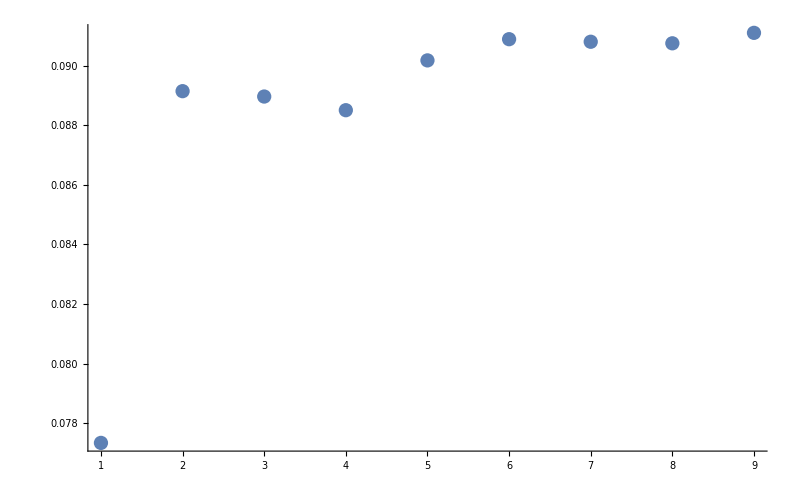
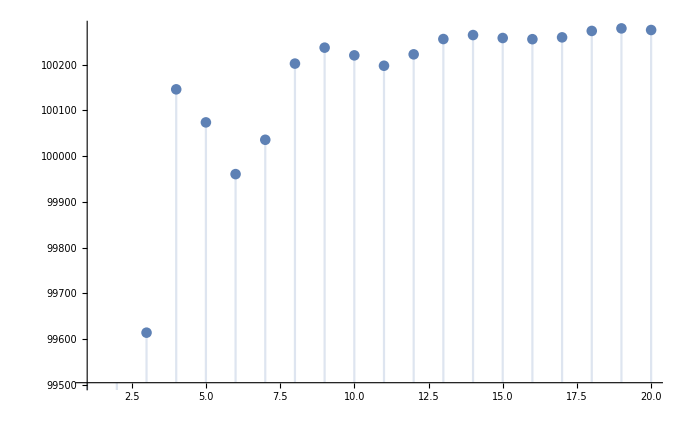
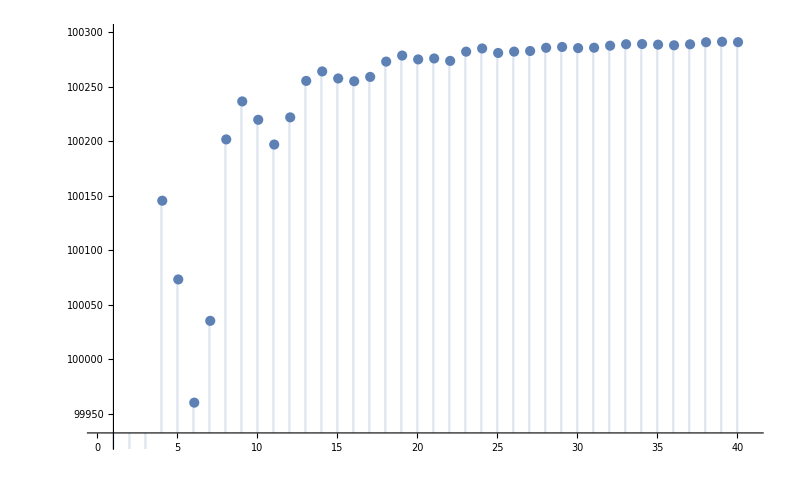
```mathematica
(* Example output of twoAnglesOptimal *)
{DateObject[{2016,8,17},TimeObject[{15,44},TimeZone->2.],TimeZone->2.],{41.80,0},7.5,8.6}

(* percentages change, first relative to the first, then to the previous *)
{0,0.0214891,0.0269413,0.0262005,0.0250416,0.025811,0.0275178,0.0278751,0.0277023}
{0,0.0214891,0.00533747,-0.000721313,-0.00112938,0.000750613,0.00166387,0.000347719,-0.000168099}

(* with -22 azimuth: *)
{0.0773427,0.0891427,0.0889624,0.088504,0.090175,0.0908864,0.0908002,0.0907483,0.0910989}
{0.0773427,0.0109529,-0.00016553,-0.000420986,0.00153513,0.000652584,-0.0000789884,-0.0000475611,0.000321402}
-Graphics--Graphics--Graphics-
```

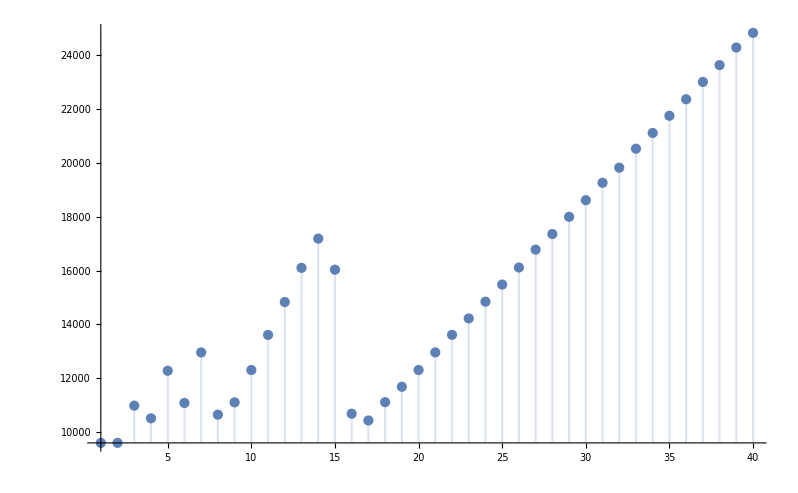
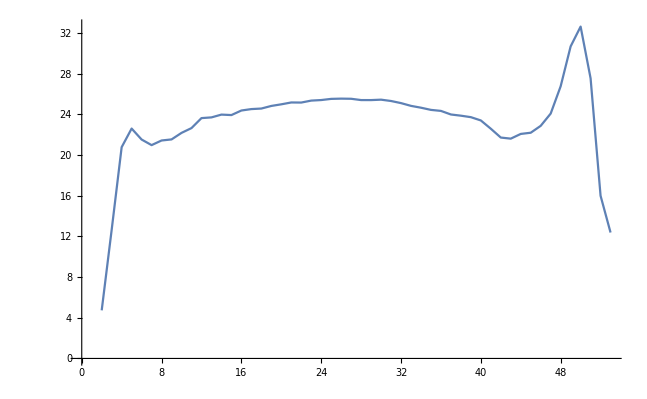
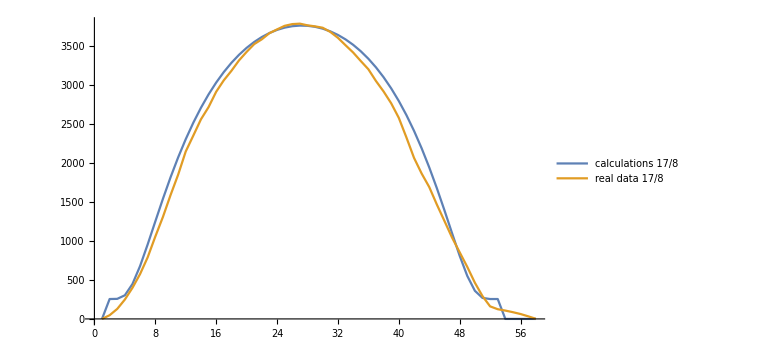
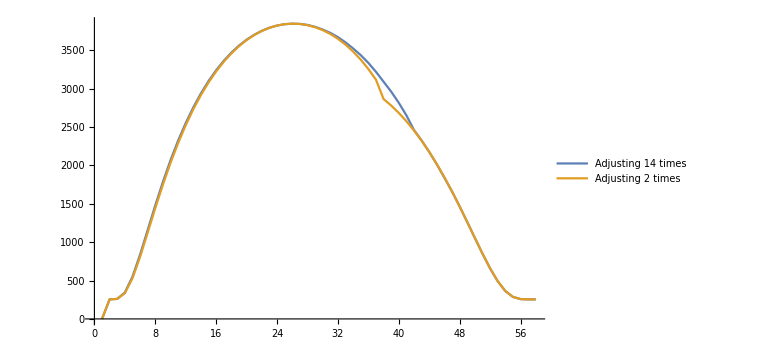
```mathematica
old -Graphics-
efficiency percentage over 17/8 -Graphics-
-Graphics-


14 times  {53.7416,51.8324,49.8813,47.5458,44.9358,42.1948,38.8167,34.4008,28.2102,18.7959,0.604448,0.,0.,0.}
-Graphics-
```